## Single Pendulum

```mathematica
SinglePendulum[w_, v0_, t_] := Module[{s, y, x},
s = NDSolve[{Sin[y[x]]+ w y''[x]==0, y[0]==0, y'[0]== v0}, y, {x, 0, t}];
Plot[y[x] /. s,{x,0,200},PlotRange->All]]
```

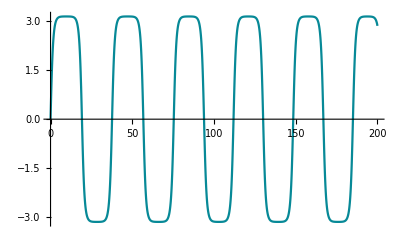

```mathematica
SinglePendulum[1.0, 1.9999999, 200]
```